```mathematica
μB=9.27400915*10^-28;
kb=1.380658*10^-23;
ℏ=6.62606896*10^-34(2π)^-1;
c=299792458;
a0 = .529*10^-10;
ϵ0 = 8.854*10^-12;
el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
Kk=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;
```

```mathematica
λ=813nm;
w0=550nm;
zr=Pi w0^2/λ;
P=1.5mW;
w[z_]:=w0(1+(z/zr)^2)^(1/2);
Ii[z_]:=P/(Pi w[z]^2/2) ;
```

```mathematica
Manipulate[Plot[(Ii[z+α zr/2]+Ii[z-α zr/2])/-2,{z,-3zr,3zr}],{α,0,2}]
```

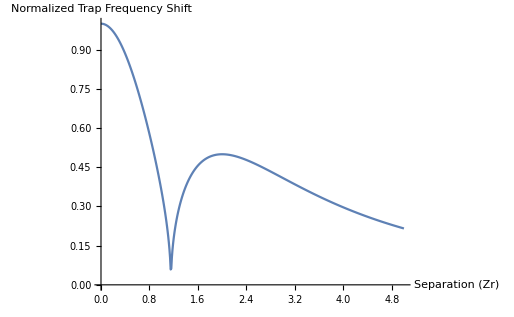

```mathematica
astigI[z_,α_]:=(Ii[z+α zr/2]+Ii[z-α zr/2])/2;
al=Range[0,5,10^-2];
trap=SeriesCoefficient[astigI[z,al],{z,0,2}];
ListPlot[Transpose[{al,Abs[√(trap/trap[[1]])]}], AxesLabel->{"Separation (Zr)","Normalized Trap Frequency Shift"},Joined->True]
```

```mathematica
√(SeriesCoefficient[astigI[z,0.68],{z,0,2}]/SeriesCoefficient[astigI[z,0],{z,0,2}])
```

0.685899

```mathematica
λ=813nm;
w0=550nm;
zr=Pi w0^2/λ;
P=1.5mW;
w[z_]:=w0(1+(z/zr)^2)^(1/2);
R[z_]:=z(1+(zr/z)^2)^(1/2);
E0[z_,α_]:=Sqrt[2P/(Pi w[z+α zr/2]w[z-α zr/2])];

η[z_,α_]:=1/2*(ArcTan[-Pi w[z-α zr/2]^2/λ*1/R[z-α zr/2]]
+ArcTan[-Pi w[z+α zr/2]^2/λ*1/R[z+α zr/2]]);

Ee[z_,α_]:=E0[z,α]Exp[I η[z,α]];
```

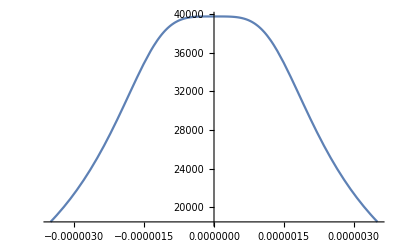

```mathematica
Plot[E0[z,2],{z,-3zr,3zr},Exclusions->z==0]
```

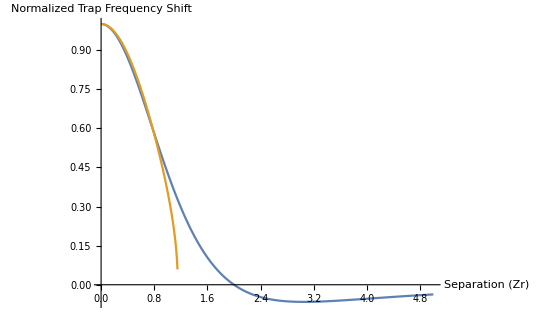

```mathematica
al=Range[0,5,10^-2];
trap2=SeriesCoefficient[E0[z,al],{z,0,2}];
ListPlot[{Transpose[{al,trap2/trap2[[1]]}],Transpose[{al,(trap/trap[[1]])^(1/2)}]}, AxesLabel->{"Separation (Zr)","Normalized Trap Frequency Shift"},Joined->True]
```

```mathematica
√(SeriesCoefficient[E0[z,0.36],{z,0,2}]/SeriesCoefficient[E0[z,0],{z,0,2}])
```

0.945231

^4